Calculation of control precision for the equation H16

```mathematica
s=2;
ep=0.1;
n=40;
c=3.5;
vq = 18;
F = Sqrt[1-J^2];
v= 31;
```

```mathematica
g1 =2 c(2n - vq + (vq/F)+(v/J)+s n-v)^2/n^2;
g2 = 2 del vq/(2n - vq + (vq/F)+(v/J)+s n-v);
g4 = del ((J+F) (vq /n) + ((vq F +2n-vq +v J +(n s - v))/n));
s ep/2
```

0.1

need to match that with the biggest del:

```mathematica
FindMinimum[{(n g1 g2 + Sqrt[n g1 g4 + (n g1 g2)^2])/.del->0.41*10^(-6),0.1<J<0.9},{J,0.5}]
```

{0.100054,{J→0.760603}}

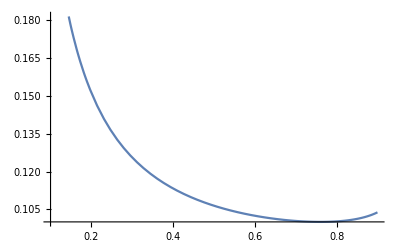

```mathematica
Plot[(n g1 g2 + Sqrt[n g1 g4 + (n g1 g2)^2])/.del->0.41*10^(-6),{J,0.1,0.9}]
```

Calculation for the equations H17-20 as well as the expressions after H7

```mathematica
SigI:={{1,0},{0,1}};(*Pauli matrices*)
SigZ:={{-1,0},{0,1}};
SigX:={{0,1},{1,0}};
SigY:={{0,-I},{I,0}};

c=2;
At[mat_,loc_]:=KroneckerProduct@@Table[If[i==loc,mat,SigI],{i,1,c}];
```

```mathematica
p0 = At[DiagonalMatrix[{0,1}],1];
p1 = At[DiagonalMatrix[{1,0}],1];
rho0 = (1/2)(At[SigI,1]- Sqrt[1-J^2] At[SigX,2] +J At[SigZ,2]);
rho1 = (1/2)(At[SigI,1]- Sqrt[1-J^2] At[SigX,2] -J At[SigZ,2]);
q0 =(1/2)(At[SigI,1]+ Sqrt[1-J^2] At[SigX,2] -J At[SigZ,2]);
q1 =(1/2)( At[SigI,1]+ Sqrt[1-J^2] At[SigX,2] +J At[SigZ,2]);
pBig = p0.rho0 + p1.rho1;
qBig=p0.q0 + p1.q1;
```

```mathematica
oper= At[SigX,1];
{Max[Abs[Eigenvalues[pBig.oper.qBig +qBig.oper.pBig]]],Max[Abs[Eigenvalues[pBig.oper.pBig ]]],Max[Abs[Eigenvalues[oper -qBig.oper.qBig]]]}
```

{Abs[J],Max[0,√Abs[1-J^2]],Max[(√Abs[1+J^2-√(1+2 J^2-3 J^4)])/(√2),(√Abs[1+J^2+√(1+2 J^2-3 J^4)])/(√2)]}

```mathematica
oper= At[SigX,2];
{Max[Abs[Eigenvalues[pBig.oper.qBig +qBig.oper.pBig]]],Max[Abs[Eigenvalues[pBig.oper.pBig ]]],Max[Abs[Eigenvalues[oper -qBig.oper.qBig]]]}
```

{Abs[J],Max[0,√Abs[1-J^2]],Max[1/2 Abs[-√(1-J^2)-√(1+3 J^2)],1/2 Abs[-√(1-J^2)+√(1+3 J^2)]]}

```mathematica
oper= At[SigZ,1];
{Max[Abs[Eigenvalues[pBig.oper.qBig +qBig.oper.pBig]]],Max[Abs[Eigenvalues[pBig.oper.pBig ]]],Max[Abs[Eigenvalues[oper -qBig.oper.qBig]]]}
```

{0,1,1}

```mathematica
oper= At[SigZ,2];
{Max[Abs[Eigenvalues[pBig.oper.qBig +qBig.oper.pBig]]],Max[Abs[Eigenvalues[pBig.oper.pBig ]]],Max[Abs[Eigenvalues[oper -qBig.oper.qBig]]]}
```

{√Abs[1-J^2],Max[0,Abs[J]],Max[1/2 Abs[-J-√(4-3 J^2)],1/2 Abs[J-√(4-3 J^2)],1/2 Abs[-J+√(4-3 J^2)],1/2 Abs[J+√(4-3 J^2)]]}

```mathematica
oper= At[SigZ,2]. At[SigZ,1];
{Max[Abs[Eigenvalues[pBig.oper.qBig +qBig.oper.pBig]]],Max[Abs[Eigenvalues[pBig.oper.pBig ]]],Max[Abs[Eigenvalues[oper -qBig.oper.qBig]]]}
```

{√Abs[1-J^2],Max[0,Abs[J]],Max[1/2 Abs[J-√(4-3 J^2)],1/2 Abs[J+√(4-3 J^2)]]}

improved control precision E30 for c=3.5 and the calculation of the iterations in c until self-consistency

```mathematica
s=2;
ep=0.1;
n=40;
c=3.5;
vq = 18;
F = Sqrt[1-J^2];
v= 31;
```

```mathematica
aJ = (√(1+J^2+√(1+2 J^2-3 J^4)))/(√2);
bJ=1/2 (√(1-J^2)+√(1+3 J^2));
cJ=1/2 (J+√(4-3 J^2));
```

```mathematica
g1 = c vq (J/F)(2n - vq + (vq aJ/F)+(v/J)+s n-v);
g2 =  del vq (Sqrt[F] + J)F/(vq J);
g3 =del vq (cJ +bJ)/(2n - vq + (vq aJ/F)+(v/J)+s n-v);
g4 = del ((J+F) (vq ) + ((vq F +2n-vq +v J +(n s - v))));
s ep/2
```

0.1

```mathematica
FindMaximum[{((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.del->3.056*10^(-5),0.01<J<0.9},{J,0.5}]
```

{0.0229729,{J→0.0687978}}

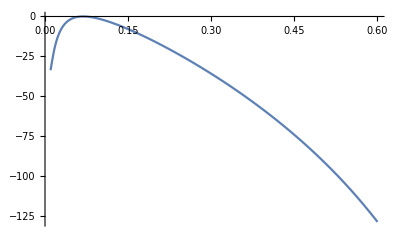

```mathematica
Plot[((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.del->3.056*10^(-5),{J,0.01,0.6}]
```

```mathematica
((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.{del->3.055*10^(-5),J-> 0.069}
```

0.0433428

```mathematica
alpp =Sqrt[(g4/g1 + g2 g3)]/.{del->3.055*10^(-5),J-> 0.069}
```

0.00135013

```mathematica
x=(del vq (Sqrt[F] + J) +alpp(vq J)/F)/.{del->3.055*10^(-5),J-> 0.069}
```

0.00226805

```mathematica
(1/x)Tan[(-1/4)Log[1-(8x/(1-2x))]]
```

2.02766

self consistent c

```mathematica
s=2;
ep=0.1;
n=40;
c=2.03;
vq = 18;
F = Sqrt[1-J^2];
v= 31;
```

```mathematica
aJ = (√(1+J^2+√(1+2 J^2-3 J^4)))/(√2);
bJ=1/2 (√(1-J^2)+√(1+3 J^2));
cJ=1/2 (J+√(4-3 J^2));
```

```mathematica
g1 = c vq (J/F)(2n - vq + (vq aJ/F)+(v/J)+s n-v);
g2 =  del vq (Sqrt[F] + J)F/(vq J);
g3 =del vq (cJ +bJ)/(2n - vq + (vq aJ/F)+(v/J)+s n-v);
g4 = del ((J+F) (vq ) + ((vq F +2n-vq +v J +(n s - v))));
s ep/2
```

0.1

```mathematica
FindMaximum[{((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.del->5.270*10^(-5),0.01<J<0.9},{J,0.5}]
```

{0.0106863,{J→0.0687966}}

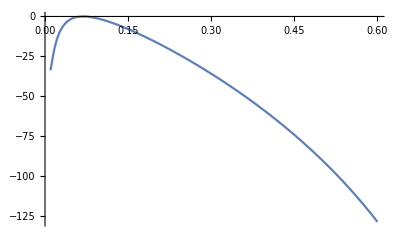

```mathematica
Plot[((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.del->5.27*10^(-5),{J,0.01,0.6}]
```

```mathematica
((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.{del->5.27*10^(-5),J-> 0.069}
```

0.0105864

```mathematica
alpp =Sqrt[(g4/g1 + g2 g3)]/.{del->5.27*10^(-5),J-> 0.069}
```

0.00232841

```mathematica
x= (del vq (Sqrt[F] + J) +alpp(vq J)/F)/.{del->5.27*10^(-5),J-> 0.069}
```

0.00391172

```mathematica
(1/x)Tan[(-1/4)Log[1-(8x/(1-2x))]]
```

2.04829

```mathematica
s=2;
ep=0.1;
n=40;
c=2.05;
vq = 18;
F = Sqrt[1-J^2];
v= 31;
```

```mathematica
aJ = (√(1+J^2+√(1+2 J^2-3 J^4)))/(√2);
bJ=1/2 (√(1-J^2)+√(1+3 J^2));
cJ=1/2 (J+√(4-3 J^2));
```

```mathematica
g1 = c vq (J/F)(2n - vq + (vq aJ/F)+(v/J)+s n-v);
g2 =  del vq (Sqrt[F] + J)F/(vq J);
g3 =del vq (cJ +bJ)/(2n - vq + (vq aJ/F)+(v/J)+s n-v);
g4 = del ((J+F) (vq ) + ((vq F +2n-vq +v J +(n s - v))));
s ep/2
```

0.1

```mathematica
FindMaximum[{((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.del->5.219*10^(-5),0.01<J<0.9},{J,0.5}]
```

{0.00571611,{J→0.0687962}}

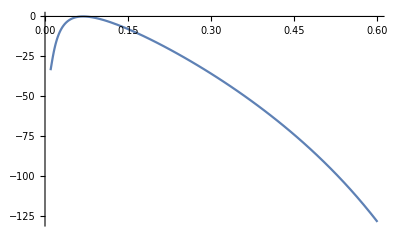

```mathematica
Plot[((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.del->5.219*10^(-5),{J,0.01,0.6}]
```

```mathematica
((g1(g2+g3) -s n ep)^2 - 4g1 g4 - 4 g1 g2 g3)/.{del->5.219*10^(-5),J-> 0.069}
```

0.00561569

```mathematica
alpp =Sqrt[(g4/g1 + g2 g3)]/.{del->5.219*10^(-5),J-> 0.069}
```

0.00230579

```mathematica
x= (del vq (Sqrt[F] + J) +alpp(vq J)/F)/.{del->5.219*10^(-5),J-> 0.069}
```

0.00387375

```mathematica
(1/x)Tan[(-1/4)Log[1-(8x/(1-2x))]]
```

2.04781